```mathematica
PlotType={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};
L=30;
```

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type*)

GT=PlotType[[p]];

data=
Table[
T=tag[[n]];(*What hashtag are we looking at*)
Table[
G[GT][T][i],{i,L}] (*Iterate over every time period*)
,{n,1,4}]; (*Iterate over each hashtag*)

Data[GT]=data; (*list of data for a given graph type in with composed of smaller list for each hashtag*)
]
```

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type basicly decomposing the previous Data*)

GT=PlotType[[p]];

fun=
Table[
Fit[
Table[
{i,Data[GT][[n]][[i]]},{i,L}](*Iterate over every time period*)
,{1,x,x^2,x^3,x^4,x^5,x^6},x](*how to find line in data*)
,{n,4}];(*iterate over each hashtag*)
Fun[GT]=fun;
]
```

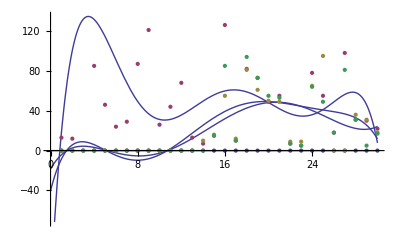
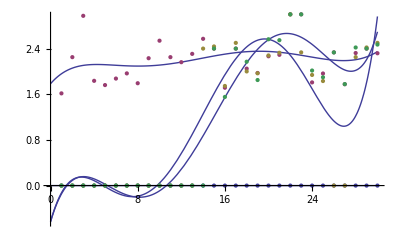
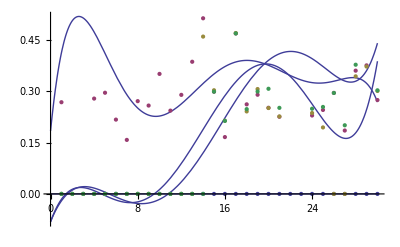
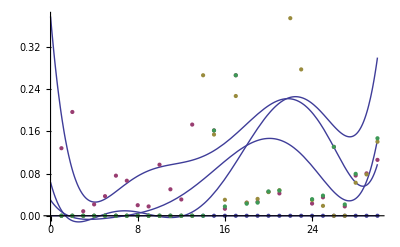
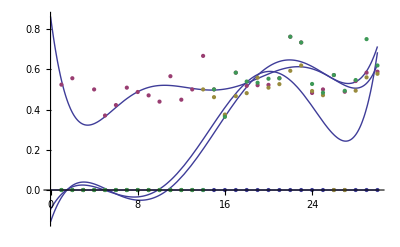
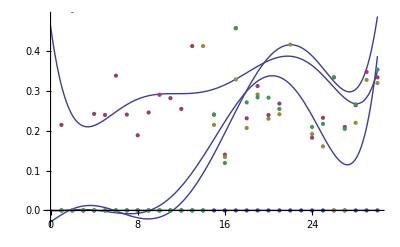
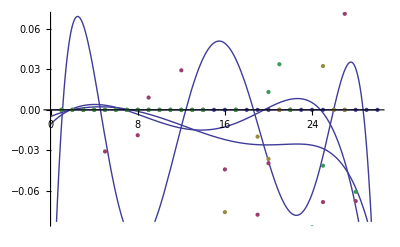
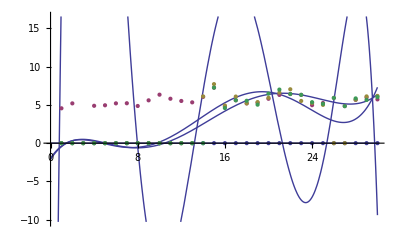

```mathematica
Table[
GT=PlotType[[p]];
bp=Plot[Fun[GT],{x,0,L}];
bpl=ListPlot[Data[GT]];
Show[bp,bpl],{p,9}]
```

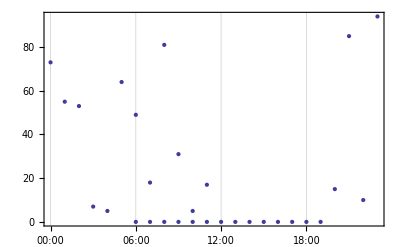

Mon06am

{{Mon06am,0},{Mon06am,13},{Mon06am,0},{Mon06am,0}}

```mathematica
Table[
Data[VC][[n]][[1]]
,{n,4}];
dt=Table[Table[
{Fdate[i],Data[VC][[n]][[i]]}
,{i,L}]
,{n,4}];
bpd=DateListPlot[dt[[4]],{Fdate[1],Fdate[L]}]
```